## Init

## Launch me

## Loading all the definitions

```mathematica
ClearAll["Global`"]
(*Specifying the mixing pattern*)
mixingPattern="e";
Tmax=50.;
TminThermo=0.01;
TminIntegration=0.015;
directoryCodes=FileNameJoin[{NotebookDirectory[],"codes"}];
Block[{Print=Identity},
Get[FileNameJoin[{directoryCodes,"asymmetries.m"}]]
]
ThermoQuantitiesC::usage
SolverAsymmetriesNoNB::usage
ThermodynamicsAndAsymmetriesTotal::usage
notev[notebook_]:=NotebookEvaluate[FileNameJoin[{directoryCodes,notebook<>".nb"}]]
Print["Load parameters, SM particles properties, thermodynamics functions:"];
Block[{Print=Identity},
notev["thermo-definitions"];
notev["kensukes-datasets"];
notev["boltzmann-equation-solver"];
notev["boltzmann-equation-solver-distribution"];
notev["plots-codes"]
];//AbsoluteTiming
```

ThermoQuantitiesC[T, ζνe, ζνμ, ζντ, ζB, ζQ] returns {ρ,s,P,ρTotCorr,ρνα,ρlα,ΔNνα,ΔNνμ,ΔNντ,ΔNνTot,ΔNlα,ΔNlμ,ΔNlτ,ΔNlTot,ΔNu,ΔNd,ΔNs,ΔNc,ΔNπ,ΔQstrong,χ2B,χ2Q,χ11,Nlα,Nlμ,Nlτ,Nνα,Nνμ,Nντ,ξπc,ΔNπ}.

SolverAsymmetriesNoNB[Tmin,Tmax,Le,Lμ,Lτ] defines the reduced neutrino and lepton asymmetries μ/T (μbehavior[x,Le,Lμ,Lτ], where x (in brackets) is e,mu,tau,ve,vmu,vtau) given the initial lepton asymmetries Le, Lmu, Ltau, assuming that the impact of sterile neutrinos is negligible.

ThermodynamicsAndAsymmetriesTotal[Tmin,Tmax,Le,Lμ,Lτ] returns the tabulated data {Tvals,Hvals,gsvals,ρvals,pvals,svals,μTνes,μTνμs,μTντs,μTes,μTμs,μTτs,μTQs,ΔLStrong,dtdTvals}, all in the units of GeV

Load parameters, SM particles properties, thermodynamics functions:

{12.2148,Null}

## Some cross-checks

### Gibbs identity

```mathematica
Print["Cross-check - Gibbs identity (p+ρ-Σ_iμ_iΔn_i)/(Ts) == 1:"]
val0=3.94;
{μTνev,μTνμv,μTντv,μTBv,μTCv}={val0,val0,0.,0.,0.9};
{μTev,μTμv,μTτv}={μTνev,μTνμv,μTντv}-μTCv;
Tv=90.;
datt=ThermoQuantitiesC[Tv,μTνev,μTνμv,μTντv,μTBv,μTCv];
{ρv,sv,pv}={Tv^4,Tv^3,Tv^4}*Take[datt,{1,3}];
{Δnev,Δnμv,Δnτv,Δnvev,Δnνμv,Δnντv,Δnπ}=Tv^3*datt[[#]]&/@{7,8,9,11,12,13,-1};
μTπ=datt[[-1]];
{μνev,μνμv,μντv,μev,μμv,μτv,μπ}=Tv{μTνev,μTνμv,μTντv,μTev,μTμv,μTτv,μTπ};
1/(Tv*sv)(pv+ρv-Total[{μνev,μνμv,μντv,μev,μμv,μτv,μπ}*{Δnev,Δnμv,Δnτv,Δnvev,Δnνμv,Δnντv,Δnπ}])
```

Cross-check - Gibbs identity (p+ρ-Σ_iμ_iΔn_i)/(Ts) == 1:

1.00629

### Zero-μ thermodynamics

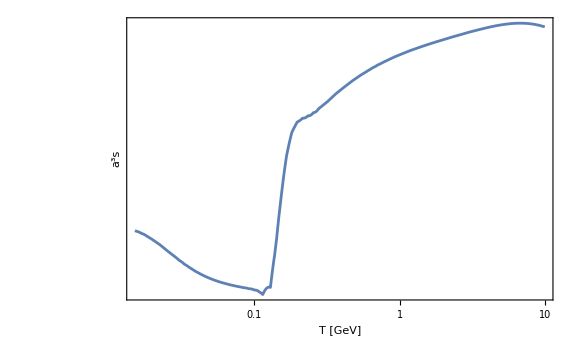

```mathematica
LogLogPlot[{aFsolSM[T]^3*sintSM[T]},{T,0.015,10},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large,FrameLabel->{"T [GeV]","a^3s"}]
```

## Launching the machinery for specific asymmetry patterns

```mathematica
(*to compute thermodynamics and sterile Boltzmann equations*)
δv=10^-4.;
keysini={{0.1,-0.1,0.},{0.1-δv,-(0.1),0.},{0.06,-0.06,0.},{0.035,-0.035,0.},{0.025,-0.025,0.},{0.015,-0.015,0.},{0.,0.06,-0.06},{0.,0.05,-0.05},{0.,0.04,-0.04},{0.,0.03,-0.03},{0.,0.02,-0.02},{0.,0.018,-0.018},{0.,0.01,-0.01},{0.,0.,0.}};
BlockDefinitions[f_]:=Module[{Lev=f[[1]],Lμv=f[[2]],Lτv=f[[3]]},
Print[Row[{{Lev,Lμv,Lτv}}]];
DefiningThermodynamics[Lev,Lμv,Lτv];
If[Max[Abs[#]&/@f]!=0.,
DefiningRHS[Lev,Lμv,Lτv];
DefiningRHS2402[Lev,Lμv,Lτv];
]
]
Do[
BlockDefinitions[f]
,{f,keysini}]
keysintegrated=Keys[DownValues@Hint][[All,1,#]]&/@{2,3,4}//Transpose
```

{0.1,-0.1,0.}

{0.0999,-0.1,0.}

{0.06,-0.06,0.}

{0.035,-0.035,0.}

{0.025,-0.025,0.}

{0.015,-0.015,0.}

{0.,0.06,-0.06}

{0.,0.05,-0.05}

{0.,0.04,-0.04}

{0.,0.03,-0.03}

{0.,0.02,-0.02}

{0.,0.018,-0.018}

{0.,0.01,-0.01}

{0.,0.,0.}

{{0.1,-0.1,0.},{0.0999,-0.1,0.},{0.06,-0.06,0.},{0.035,-0.035,0.},{0.025,-0.025,0.},{0.015,-0.015,0.},{0.,0.06,-0.06},{0.,0.05,-0.05},{0.,0.04,-0.04},{0.,0.03,-0.03},{0.,0.02,-0.02},{0.,0.018,-0.018},{0.,0.01,-0.01},{0.,0.,0.}}

### Various plots

Chemical potentials plot:

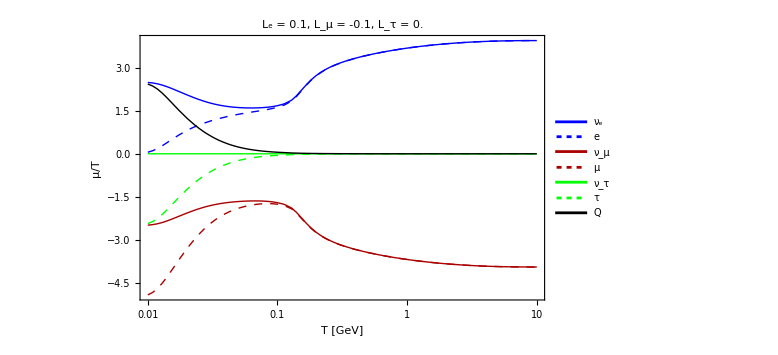

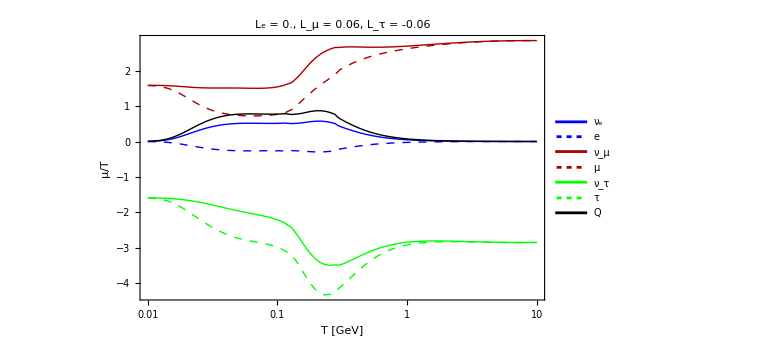

Cross-checks:

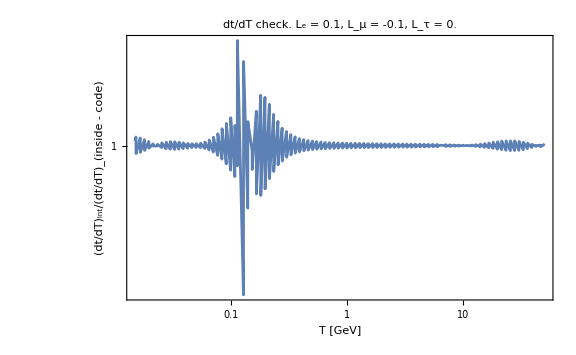
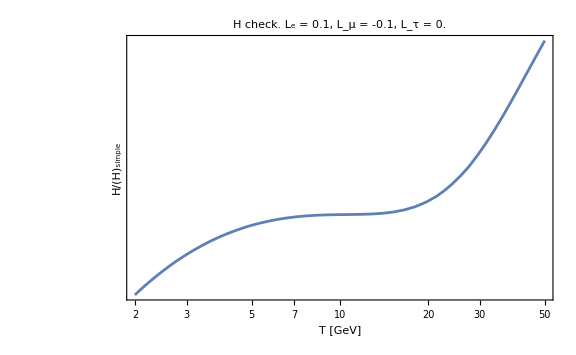
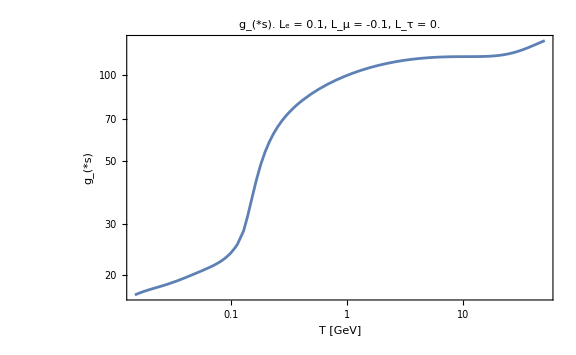
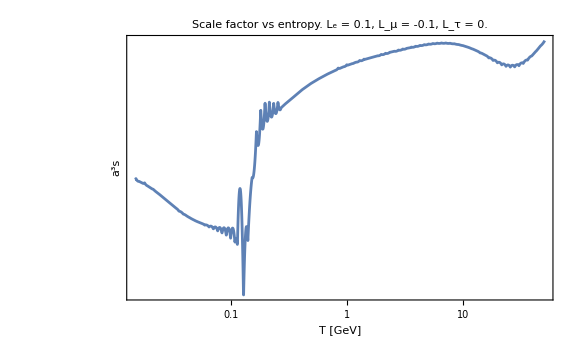

Comparison with Kensuke:

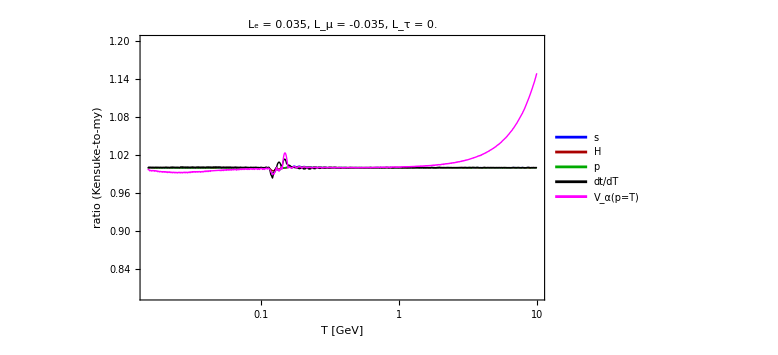
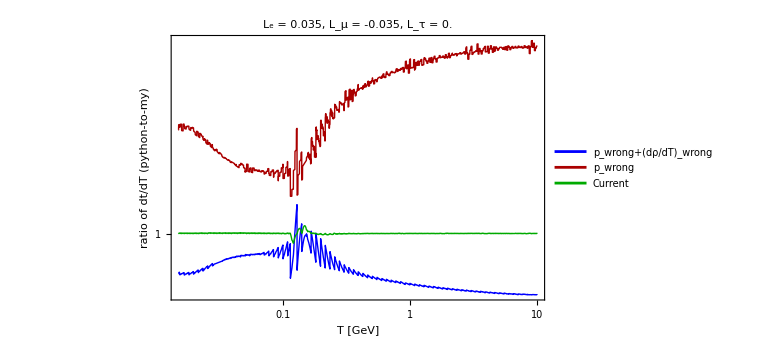

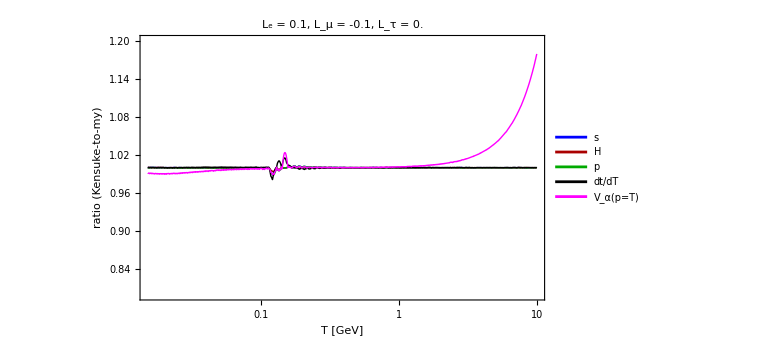
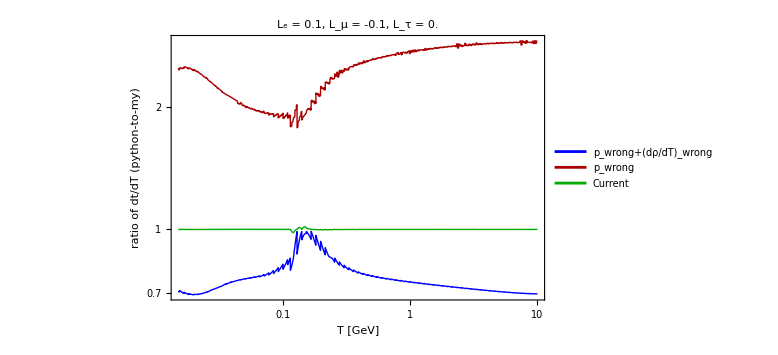

```mathematica
Print["Chemical potentials plot:"]
ptChemicalPotential[0.1,-0.1,0.]
ptChemicalPotential[0.,0.06,-0.06]
Print["Cross-checks:"];
ptCrossCheck[0.1,-0.1,0.]
Print["Comparison with Kensuke:"]
plotsKensuke[0.035,-0.035,0.]
plotsKensuke[0.1,-0.1,0.]
```

#### Resonant momenta plot

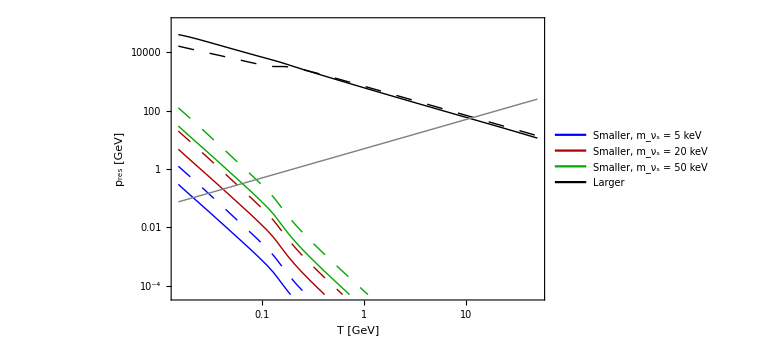

C:\Users\miksi\Dropbox\Science 2\Cosmology\Sterile DM\plots\pres.pdf

```mathematica
plotpres=LogLogPlot[Evaluate[{presν2Inserted[5,T,0.1,-0.1,0.],presν2Inserted[20,T,0.1,-0.1,0.],presν2Inserted[50,T,0.1,-0.1,0.],presν1Inserted[50,T,0.1,-0.1,0.],presν2Inserted[5,T,0.035,-0.035,0.],presν2Inserted[20,T,0.035,-0.035,0.],presν2Inserted[50,T,0.035,-0.035,0.],presν1Inserted[50,T,0.035,-0.035,0.],5T}],{T,0.015,Tmax},PlotRange->{{0.015,Tmax},{50*10^-6,100000}},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large,PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Green},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Green,Dashing[0.02]},{Thick,Black,Dashing[0.02]},{Thick,Gray}},PlotLegends->Placed[Join[Style[Row[{"Smaller, m_ν_s = ",#," keV"}],18,Black]&/@{5,20,50},{Style[Row[{"Larger"}],18,Black]}],{0.75,0.2}],FrameLabel->{"T [GeV]","p_res [GeV]"}]
Export[FileNameJoin[{NotebookDirectory[],"plots","pres.pdf"}],plotpres]
```

## Some applications

### Accumulation of the number density

{9.742×10^-48,1.00208}

{9.73286×10^-48,1.00114}

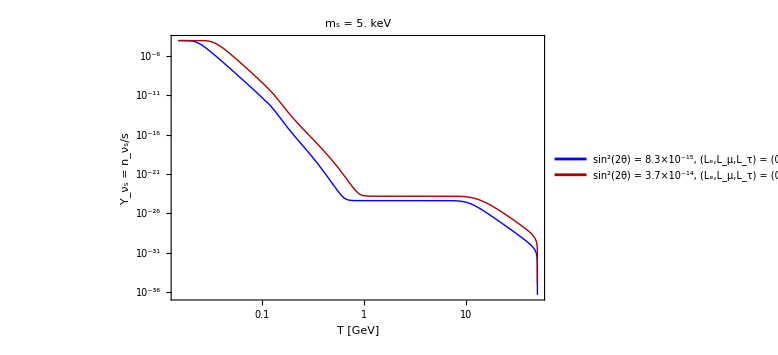

C:\Users\miksi\Dropbox\Science 2\Cosmology\Sterile DM\plots\number-density-to-entropy-behavior.pdf

{0.0999,-0.1,0.}

{4.34828×10^-47,4.47274}

```mathematica
mtest=5.;
U2test=0.832*10^-14;
{Letest,Lμtest,Lτtest}={0.1,-0.1,0.};
descr1=Row[{"sin^2(2θ) = ",ScientificForm[U2test,2],", (L_e,L_μ,L_τ) = (",Letest,",",Lμtest,",",Lτtest,")"}];
BoltzmannSolverNumberDensityDiff[mtest,U2test,Letest,Lμtest,Lτtest]
{Letest,Lμtest,Lτtest}={0.035,-0.035,0.};
U2test=0.83*10^-14*(0.1/0.035)^1.43;
descr2=Row[{"sin^2(2θ) = ",ScientificForm[U2test,2],", (L_e,L_μ,L_τ) = (",Letest,",",Lμtest,",",Lτtest,")"}];
BoltzmannSolverNumberDensityDiff[mtest,U2test,Letest,Lμtest,Lτtest]
ptabundance=LogLogPlot[{YνsTotSol[mtest,T,0.1,-0.1,0.],YνsTotSol[mtest,T,0.035,-0.035,0.]},{T,TminIntegration,Tmax},PlotRange->{{TminIntegration,Tmax},All},Frame->True,FrameStyle->Directive[Thick,Black,20],ImageSize->Large,FrameLabel->{"T [GeV]","Y_ν_s = n_ν_s/s"},PlotLegends->Placed[Style[Row[{#}],16,Black]&/@{descr1,descr2},{0.46,0.2}],PlotLabel->Style[Row[{"m_s = ",mtest//N," keV"}],18,Black],PlotStyle->{{Thick,Blue},{Thick,Darker@Red}}]
Export[FileNameJoin[{NotebookDirectory[],"plots","number-density-to-entropy-behavior.pdf"}],ptabundance]
{Letest,Lμtest,Lτtest}=keysintegrated[[2]]
BoltzmannSolverNumberDensityDiff[mtest,U2test,Letest,Lμtest,Lτtest]
```

### Check back-reaction

```mathematica
Print["Present entropy density s_today in MeV^3:"]
sTtoday*10^9
Print["Present DM energy density ρ_(DM, today) in MeV^4"]
0.265*ρcritical*10^12
Print["Sterile neutrino abundance L_ν_s = n_s/s required to explain the DM as a function of sterile mass in keV, L_ν_s×s_today×m_ν_s = ρ_(DM, today):"]
LνsRequired[ms_]=Lνs/.Solve[(ms*10^-6)*Lνs*sTtoday==0.265*ρcritical,Lνs][[1]]
Print["The value of L_ν_s for m_s = 5 keV:"]
LνsRequired[5.]
```

Present entropy density s_today in MeV^3:

2.23462×10^-29

Present DM energy density ρ_(DM, today) in MeV^4

9.72173×10^-36

Sterile neutrino abundance L_ν_s = n_s/s required to explain the DM as a function of sterile mass in keV, L_ν_s×s_today×m_ν_s = ρ_(DM, today):

0.000435052/ms

The value of L_ν_s for m_s = 5 keV:

0.0000870103

### Comparison with Kensuke

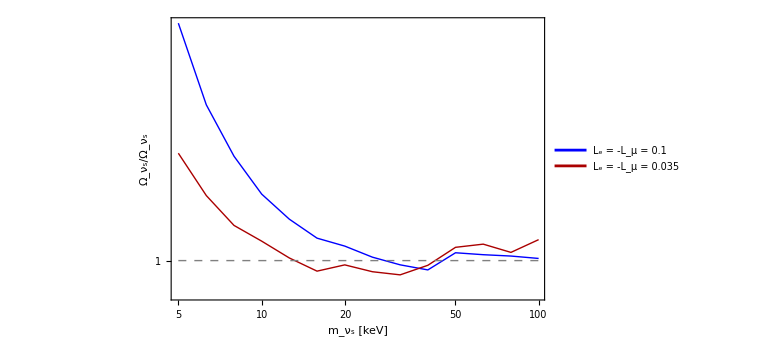

C:\Users\miksi\Dropbox\Science 2\Cosmology\Sterile DM\plots\Deviation.pdf

```mathematica
tabdeviations01=ResourceFunction["MonitorProgress"]@({#[[1]],#[[2]],(BoltzmannSolverNumberDensityInt[#[[1]],#[[2]],0.1,-0.1,0.][[2]])}&/@datakensuke01);
tabdeviations0035=ResourceFunction["MonitorProgress"]@({#[[1]],#[[2]],(BoltzmannSolverNumberDensityInt[#[[1]],#[[2]],0.035,-0.035,0.][[2]])}&/@datakensuke0035);
ptdeviation=ListLogLogPlot[{tabdeviations01[[All,{1,3}]],tabdeviations0035[[All,{1,3}]],Table[{x,1.},{x,5,100,1.}]},Joined->True,PlotRange->{{5.,99},All},Frame->True,FrameStyle->Directive[Thick,Black,20],FrameLabel->{"m_ν_s [keV]","Ω_ν_s/Ω_ν_s"}(*,PlotLabel->Style[Row[{"L_e = -L_μ = 0.1"}],18,Black]*),ImageSize->Large,PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Gray,Dashing[0.01]}},PlotLegends->Placed[Style[Row[{#}],20,Black]&/@{"L_e = -L_μ = 0.1","L_e = -L_μ = 0.035"},{0.8,0.8}]]
(*tabdeviations0035=ResourceFunction["MonitorProgress"]@({#[[1]],#[[2]],DynamicsnsρsIntTruncated[#[[1]],#[[2]],0.35Letest,0.35Lμtest,0.][[2]]}&/@datakensuke0035);*)
Export[FileNameJoin[{NotebookDirectory[],"plots","Deviation.pdf"}],ptdeviation]
```

### Distribution plot

InterpolatingFunction::dmval: Input value {-4.20976} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

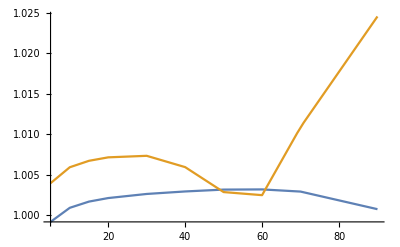

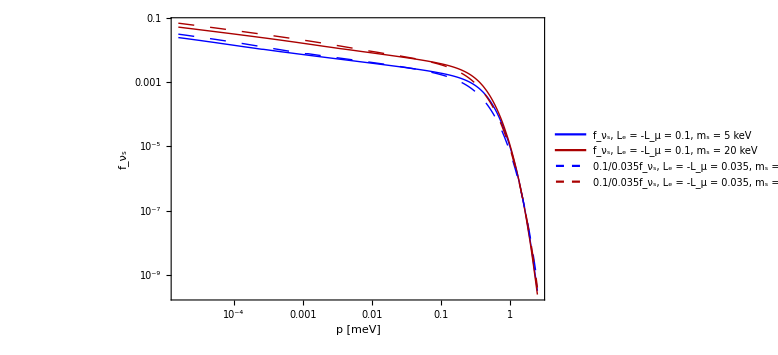

C:\Users\miksi\Dropbox\Science 2\Cosmology\Sterile DM\plots\Energy-spectrum.pdf

1.07736

```mathematica
Let=0.1;
Lμt=-Let;
Lτt=0.;
tbbb01=ResourceFunction["MonitorProgress"]@Table[{mst,BoltzmannSolverDistribution[mst,10^-14,Let,Lμt,Lτt]/(BoltzmannSolverNumberDensityInt[mst,10^-14,Let,Lμt,Lτt][[2]])},{mst,{5,10,15,20,30,40,50,60,70,90}}];
tbbb01Int[ms_]=Interpolation[tbbb01,InterpolationOrder->1][ms];
Let=0.035;
Lμt=-Let;
Lτt=0.;
tbbb0035=ResourceFunction["MonitorProgress"]@Table[{mst,BoltzmannSolverDistribution[mst,10^-14,Let,Lμt,Lτt]/(BoltzmannSolverNumberDensityInt[mst,10^-14,Let,Lμt,Lτt][[2]])},{mst,{5,10,15,20,30,40,50,60,70,90}}];
tbbb0035Int[ms_]=Interpolation[tbbb0035,InterpolationOrder->1][ms];
Plot[{tbbb01Int[ms],tbbb0035Int[ms]},{ms,5,90},PlotRange->All];
(*LogLogPlot[IntegrandRHSdistr[y,Lev,Lμv,Lτv],{y,Min[ygridDistr],Max[ygridDistr]},Frame->True,FrameStyle->Directive[Thick,Black,22],ImageSize->Large,PlotStyle->({Thick,#}&/@{Blue,Darker@Red,Darker@Darker@Green})]*)
ptspectrum=LogLogPlot[{IntegrandRHSdistrToday[5,10^-12 p,0.1,-0.1,0.],IntegrandRHSdistrToday[20,10^-12 p,0.1,-0.1,0.],IntegrandRHSdistrToday[5,10^-12 p,0.035,-0.035,0.] 0.1/0.035,IntegrandRHSdistrToday[20,10^-12 p,0.035,-0.035,0.] 0.1/0.035},{p,10^12 pminToday[Lev,Lμv,Lτv],10^12 pmaxToday[Lev,Lμv,Lτv]},Frame->True,PlotRange->{{10^12 pminToday[Lev,Lμv,Lτv],10^12 pmaxToday[Lev,Lμv,Lτv]},All},FrameStyle->Directive[Thick,Black,22],FrameLabel->{"p [meV]","f_ν_s"},ImageSize->Large,PlotStyle->(Join[{Thick,#}&/@{Blue,Darker@Red},{Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red}]),PlotLegends->Placed[Style[Row[{#}],18,Black]&/@{"f_ν_s, L_e = -L_μ = 0.1, m_s = 5 keV","f_ν_s, L_e = -L_μ = 0.1, m_s = 20 keV","0.1/0.035f_ν_s, L_e = -L_μ = 0.035, m_s = 5 keV","0.1/0.035f_ν_s, L_e = -L_μ = 0.035, m_s = 20 keV"},{0.38,0.3}]]
Export[FileNameJoin[{NotebookDirectory[],"plots","Energy-spectrum.pdf"}],ptspectrum]
```

### Distributions - comparison with Kensuke

#### Data import

```mathematica
mlpairs={{20.,0.1},{50.,0.1},{20.,0.01},{50.,0.01}};
ResourceFunction["MonitorProgress"]@Do[
Module[{m=f[[1]],l=f[[2]]},
distrKensuke[m,l]=Import[FileNameJoin[{NotebookDirectory[],"data","fnus_Lemu_"<>StringReplace[ToString[l],"."->""]<>"_"<>ToString[m//IntegerPart]<>".txt"}],"CSV"];
distrKensukeInt[m,l,p_]=Interpolation[distrKensuke[m,l],InterpolationOrder->1][p];
BoltzmannSolverDistribution[m,3.77*10^-15*(10/m)^1.45*(0.1/l)^1.25,l,-l,0.];
]
,{f,mlpairs}]
```

{0.01,-0.01,0.}

#### Plots with comparison

InterpolatingFunction::dmval: Input value {0.00029365} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

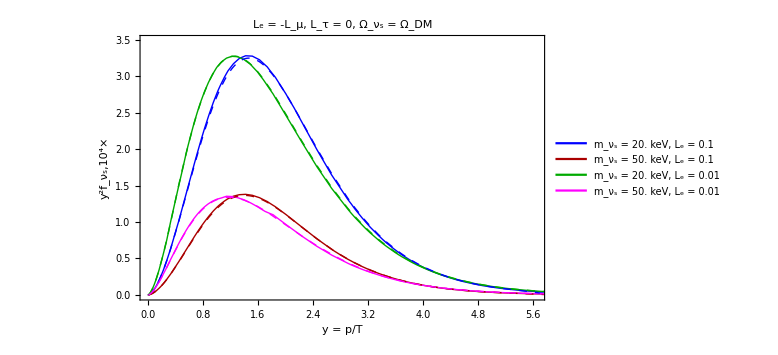

C:\Users\miksi\Dropbox\Science 2\Cosmology\Sterile DM\plots\distr-comparison.pdf

```mathematica
ptspectrum=Plot[Evaluate[10^4{p^2 IntegrandRHSdistrToday[20.,Ttoday*p,0.1,-0.1,0.],p^2 IntegrandRHSdistrToday[50.,Ttoday*p,0.1,-0.1,0.]/0.96,p^2 IntegrandRHSdistrToday[20.,Ttoday*p,0.01,-0.01,0.]/1.23,p^2 IntegrandRHSdistrToday[50.,Ttoday*p,0.01,-0.01,0.]/1.12,distrKensukeInt[20.,0.1,p],distrKensukeInt[50.,0.1,p],distrKensukeInt[20.,0.01,p],distrKensukeInt[50.,0.01,p]}],{p,pminToday[Lev,Lμv,Lτv]/Ttoday,pmaxToday[Lev,Lμv,Lτv]/Ttoday},Frame->True,PlotRange->{{10^12 pminToday[Lev,Lμv,Lτv],2.19*10^12 pmaxToday[Lev,Lμv,Lτv]},{0.,3.49}},FrameStyle->Directive[Thick,Black,22],FrameLabel->{"y = p/T","y^2f_ν_s,10^4×"},ImageSize->Large,PlotStyle->(Join[{Thick,#}&/@{Blue,Darker@Red,Darker@Green,Magenta},{Thick,#,Dashing[0.01]}&/@{Blue,Darker@Red,Darker@Green,Magenta}]),PlotLegends->Placed[Style[Row[{"m_ν_s = ",#[[1]]," keV, L_e = ",#[[2]]}],18,Black]&/@mlpairs,{0.75,0.75}],PlotLabel->Style[Row[{"L_e = -L_μ, L_τ = 0, Ω_ν_s = Ω_DM"}],20,Black]]
Export[FileNameJoin[{NotebookDirectory[],"plots","distr-comparison.pdf"}],ptspectrum]
```

### Scaling Ω_ν_s(L)

#### Mixing with ν_e

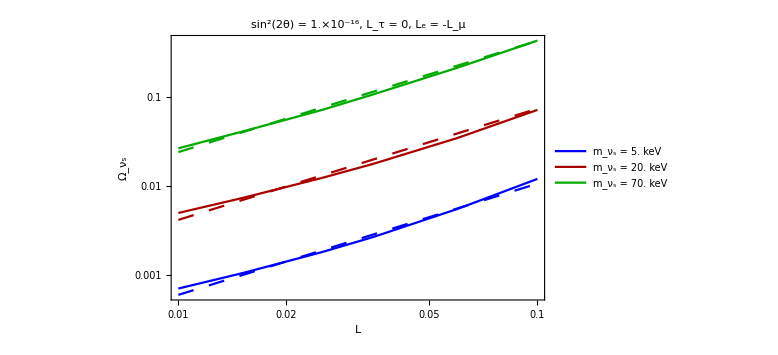
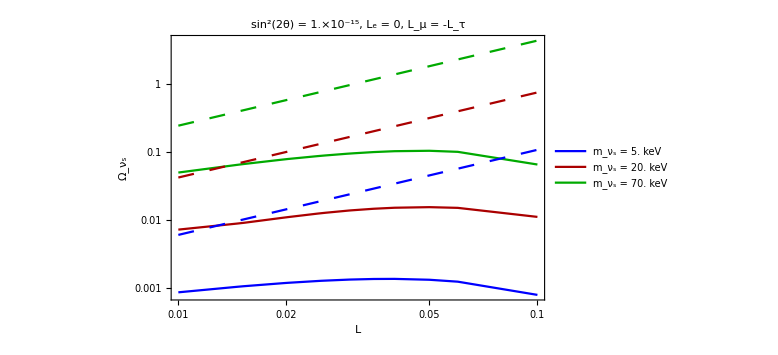

```mathematica
If[mixingPattern=="e",
Levals=Select[keysintegrated,#[[3]]==0.&&!MemberQ[{0.,0.0999},#[[1]]]&][[All,1]]//Sort;
mvs={5.,20.,70.};
U2t=10^-16.;
tabbvs=Flatten[ResourceFunction["MonitorProgress"]@Table[{mtest,Letest,U2t,BoltzmannSolverNumberDensityInt[mtest,U2t,Letest,-Letest,0.][[2]]},{mtest,mvs},{Letest,Levals}],1]//N;
Do[
intLeScaling[m,Le_]=Interpolation[Select[tabbvs,#[[1]]==m&][[All,{2,4}]]//Log,InterpolationOrder->1][Log[Le]]//Exp;
,{m,mvs}];
fitfLe[Le_,mνs_]=0.04*(Le/0.015)^1.25*(mνs/70.)^1.4;
plotAbundanceLe=LogLogPlot[Evaluate[Join[intLeScaling[#,Le]&/@mvs,(fitfLe[Le,#])&/@mvs]],{Le,Min[Levals],Max[Levals]},PlotRange->{{Min[Levals],Max[Levals]},All},ImageSize->Large,Frame->True,FrameLabel->{"L","Ω_ν_s"},FrameStyle->Directive[Thick,Black,20],PlotStyle->Join[{Thick,#}&/@{Blue,Darker@Red,Darker@Green},{Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green}],PlotLabel->Style[Row[{"sin^2(2θ) = ",ScientificForm[U2t,1],", L_τ = 0, L_e = -L_μ"}],18,Black],PlotLegends->Placed[Style[Row[{"m_ν_s = ",#," keV"}],18,Black]&/@mvs,{0.84,0.17}]];
Export[FileNameJoin[{NotebookDirectory[],"plots","Abundance-scaling.pdf"}],plotAbundanceLe];
Lμvals=Select[keysintegrated,#[[1]]==0.&&!MemberQ[{0.,0.018},#[[2]]]&][[All,2]]//Sort;
mvs={5.,20.,70.};
U2t=10^-15.;
tabbvs=Flatten[ResourceFunction["MonitorProgress"]@Table[{mtest,Letest,U2t,BoltzmannSolverNumberDensityInt[mtest,U2t,0.,Letest,-Letest][[2]]},{mtest,mvs},{Letest,Lμvals}],1]//N;
Do[
intLμScaling[m,Le_]=Interpolation[Select[tabbvs,#[[1]]==m&][[All,{2,4}]]//Log,InterpolationOrder->1][Log[Le]]//Exp;
,{m,mvs}];
plotAbundanceLμ=LogLogPlot[Evaluate[Join[intLμScaling[#,Lμ]&/@mvs,(10*0.04*(Lμ/0.015)^1.25*(#/70.)^1.4)&/@mvs]],{Lμ,Min[Lμvals],Max[Lμvals]},PlotRange->{{Min[Lμvals],Max[Lμvals]},All},ImageSize->Large,Frame->True,FrameLabel->{"L","Ω_ν_s"},FrameStyle->Directive[Thick,Black,20],PlotStyle->Join[{Thick,#}&/@{Blue,Darker@Red,Darker@Green},{Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green}],PlotLabel->Style[Row[{"sin^2(2θ) = ",ScientificForm[U2t,1],", L_e = 0, L_μ = -L_τ"}],18,Black],PlotLegends->Placed[Style[Row[{"m_ν_s = ",#," keV"}],18,Black]&/@mvs,{0.8,0.2}]];
Export[FileNameJoin[{NotebookDirectory[],"plots","Abundance-scaling-Lmu.pdf"}],plotAbundanceLμ];
Style[Row[{plotAbundanceLe,plotAbundanceLμ}],ImageSizeMultipliers->{1,0.5}]
]
```

#### Mixing with ν_μ

InterpolatingFunction::dmval: Input value {-4.60513} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

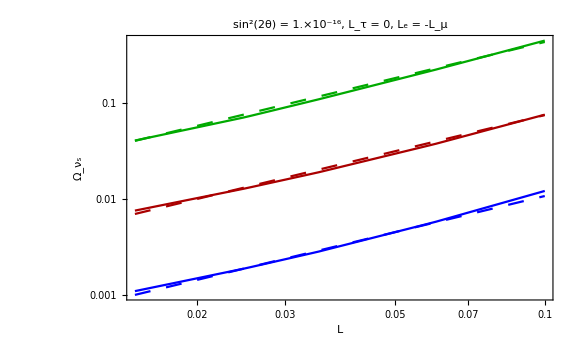
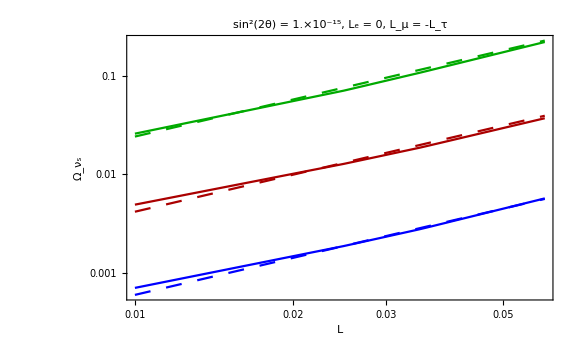

```mathematica
If[mixingPattern=="μ",
Levals=Select[keysintegrated,#[[3]]==0.&&!MemberQ[{0.,0.0999},#[[1]]]&][[All,1]]//Sort;
mvs={5.,20.,70.};
U2t=10^-16.;
tabbvs=Flatten[ResourceFunction["MonitorProgress"]@Table[{mtest,Letest,U2t,BoltzmannSolverNumberDensityInt[mtest,U2t,Letest,-Letest,0.][[2]]},{mtest,mvs},{Letest,Levals}],1]//N;
Do[
intLeScaling[m,Le_]=Interpolation[Select[tabbvs,#[[1]]==m&][[All,{2,4}]]//Log,InterpolationOrder->1][Log[Le]]//Exp;
,{m,mvs}];
fitfLe[Le_,mνs_]=0.04*(Le/0.015)^1.25*(mνs/70.)^1.4;
plotAbundanceLe=LogLogPlot[Evaluate[Join[intLeScaling[#,Le]&/@mvs,(fitfLe[Le,#])&/@mvs]],{Le,Min[Levals],Max[Levals]},PlotRange->{{Min[Levals],Max[Levals]},All},ImageSize->Large,Frame->True,FrameLabel->{"L","Ω_ν_s"},FrameStyle->Directive[Thick,Black,20],PlotStyle->Join[{Thick,#}&/@{Blue,Darker@Red,Darker@Green},{Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green}],PlotLabel->Style[Row[{"sin^2(2θ) = ",ScientificForm[U2t,1],", L_τ = 0, L_e = -L_μ"}],18,Black]];
Export[FileNameJoin[{NotebookDirectory[],"plots","Abundance-scaling.pdf"}],plotAbundanceLe];
Lμvals=Select[keysintegrated,#[[1]]==0.&&!MemberQ[{0.,0.018},#[[2]]]&][[All,2]]//Sort;
mvs={5.,20.,70.};
U2t=10^-15.;
tabbvs=Flatten[ResourceFunction["MonitorProgress"]@Table[{mtest,Letest,U2t,BoltzmannSolverNumberDensityInt[mtest,U2t,Letest,-Letest,0.][[2]]},{mtest,mvs},{Letest,Levals}],1]//N;
Do[
intLμScaling[m,Le_]=Interpolation[Select[tabbvs,#[[1]]==m&][[All,{2,4}]]//Log,InterpolationOrder->1][Log[Le]]//Exp;
,{m,mvs}];
plotAbundanceLμ=LogLogPlot[Evaluate[Join[intLeScaling[#,Lμ]&/@mvs,(0.04*(Lμ/0.015)^1.25*(#/70.)^1.4)&/@mvs]],{Lμ,Min[Lμvals],Max[Lμvals]},PlotRange->{{Min[Lμvals],Max[Lμvals]},All},ImageSize->Large,Frame->True,FrameLabel->{"L","Ω_ν_s"},FrameStyle->Directive[Thick,Black,20],PlotStyle->Join[{Thick,#}&/@{Blue,Darker@Red,Darker@Green},{Thick,#,Dashing[0.02]}&/@{Blue,Darker@Red,Darker@Green}],PlotLabel->Style[Row[{"sin^2(2θ) = ",ScientificForm[U2t,1],", L_e = 0, L_μ = -L_τ"}],18,Black]];
Export[FileNameJoin[{NotebookDirectory[],"plots","Abundance-scaling-Lmu.pdf"}],plotAbundanceLμ];
Style[Row[{plotAbundanceLe,plotAbundanceLμ}],ImageSizeMultipliers->{1,0.5}]
]
```